```mathematica
A=({{-1/2, -1, -1}, {2, 7/2, 3}, {-1, -2, -3/2}})
```

{{-1/2,-1,-1},{2,7/2,3},{-1,-2,-3/2}}

Mi calcolo gli autovalori di A

```mathematica
λ=Eigenvalues[A]
```

{1/2,1/2,1/2}

Mi calcolo la molteplicita’ geometrica di questo autovalore “triplo”, dim(Ker(A - lambda I))

```mathematica
NullSpace[A-1/2 IdentityMatrix[3]]
```

{{0,-1,1}}

```mathematica
Simplify[ResourceFunction["MatrixMinimalPolynomial"][A,x]]
```

1/8 (-1+2 x)^3

In questo caso i modi naturali sono 3 (molteplicita’ dell’autovalore nel polinomio minimo). 
Vediamo i grafici delle successioni polinomial-potenza

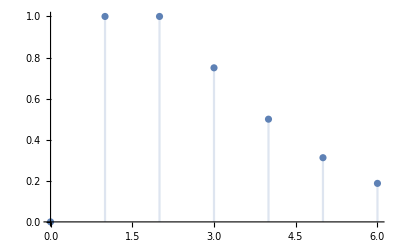

```mathematica
DiscretePlot[Binomial[k,1] (1/2)^(k-1),{k,0,6}]
```

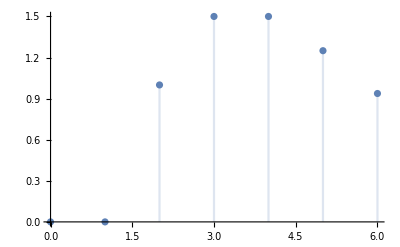

```mathematica
DiscretePlot[Binomial[k,2] (1/2)^(k-2),{k,0,6}]
```